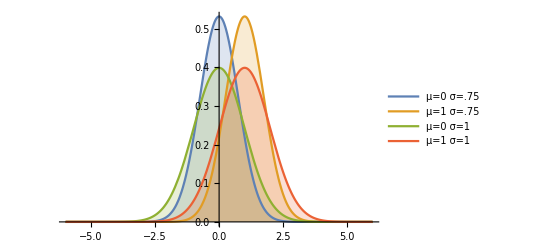

```mathematica
Plot[Table[PDF[NormalDistribution[μ,σ],x],{σ,{.75,1}},{μ,{0,1}}]//Evaluate,{x,-6,6},Filling->Axis, PlotLegends->{"μ=0 σ=.75","μ=1 σ=.75","μ=0 σ=1", "μ=1 σ=1"}]
```

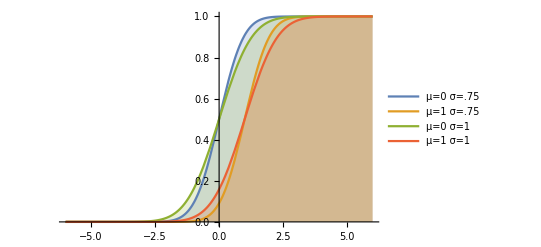

```mathematica
Plot[Table[CDF[NormalDistribution[μ,σ],x],{σ,{.75,1}},{μ,{0,1}}]//Evaluate,{x,-6,6},Filling->Axis, PlotLegends->{"μ=0 σ=.75","μ=1 σ=.75","μ=0 σ=1", "μ=1 σ=1"}]
```

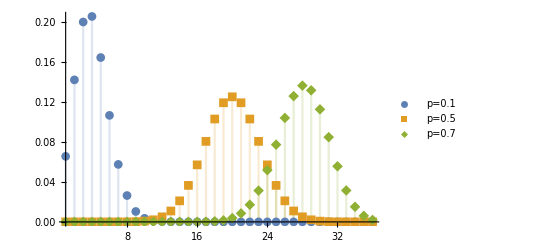

```mathematica
DiscretePlot[Table[PDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.7}}]//Evaluate,{k,36},PlotRange->All,PlotMarkers->Automatic,PlotLegends->{"p=0.1","p=0.5","p=0.7"}]
```

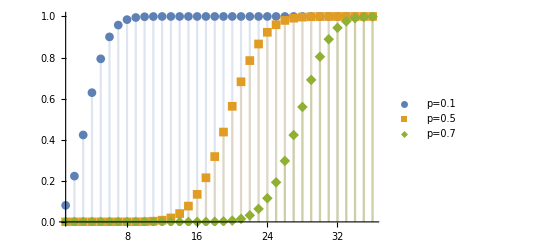

```mathematica
DiscretePlot[Table[CDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.7}}]//Evaluate,{k,36},PlotRange->All,PlotMarkers->Automatic,PlotLegends->{"p=0.1","p=0.5","p=0.7"}]
```